# Predicting Office Occupancy

Preprocessing

Read occupancy dataset. Please find dataset here: 
https://github.com/LuisM78/Occupancy-detection-data
OfficeOccupancy is dataset2.txt

```mathematica
officeOccupancy = Import["Path/officeOccupancy.csv","CSV"]
```

```mathematica
officeOccupancy[[1;;5]]
```

{{date,Temperature,Humidity,Light,CO2,HumidityRatio,Occupancy},{2/11/15 14:48,21.76,31.1333,437.333,1029.67,0.00502101,1},{2/11/15 14:49,21.79,31,437.333,1000,0.00500858,1},{2/11/15 14:50,21.7675,31.1225,434,1003.75,0.00502157,1},{2/11/15 14:51,21.7675,31.1225,439,1009.5,0.00502157,1}}

```mathematica
TableForm[%249]
```

date | Temperature | Humidity | Light | CO2 | HumidityRatio | Occupancy
2/11/15 14:48 | 21.76 | 31.1333 | 437.333 | 1029.67 | 0.00502101 | 1
2/11/15 14:49 | 21.79 | 31 | 437.333 | 1000 | 0.00500858 | 1
2/11/15 14:50 | 21.7675 | 31.1225 | 434 | 1003.75 | 0.00502157 | 1
2/11/15 14:51 | 21.7675 | 31.1225 | 439 | 1009.5 | 0.00502157 | 1

Separate the date from time, and create the new dataset

```mathematica
officeOccupancyData = Map[Join[StringSplit[First[#]],Rest[#]]&,Rest[officeOccupancy]]
```

{{2/11/15,14:48,21.76,31.1333,437.333,1029.67,0.00502101,1},{2/11/15,14:49,21.79,31,437.333,1000,0.00500858,1},9748,{2/18/15,9:17,20.89,28.0225,418.75,1632,0.00427949,1},{2/18/15,9:19,21,28.1,409,1864,0.00432073,1}}
 |  |  |  |

remove Humidity Ration

```mathematica
officeOccupancyData = officeOccupancyData[[All,{1,2,3,4,5,6,8}]]
```

Create subsets based on the date

```mathematica
office21611 =Select[officeOccupancyData,StringMatchQ [First[#],"2/11/15"]&][[All,{3,4,5,6,7}]];
validateDate11= Map[Rule[Most[#],Last[#]]&,office21611];
office21612=Select[officeOccupancyData,StringMatchQ [First[#],"2/12/15"]&][[All,{3,4,5,6,7}]];
validateDate12 = Map[Rule[Most[#],Last[#]]&,office21612];
office21613=Select[officeOccupancyData,StringMatchQ [First[#],"2/13/15"]&][[All,{3,4,5,6,7}]];
validateDate13 = Map[Rule[Most[#],Last[#]]&,office21613];
office21614 =Select[officeOccupancyData,StringMatchQ [First[#],"2/14/15"]&][[All,{3,4,5,6,7}]];
validateDate14= Map[Rule[Most[#],Last[#]]&,office21614];
office21615 =Select[officeOccupancyData,StringMatchQ [First[#],"2/15/15"]&][[All,{3,4,5,6,7}]];
validateDate15 = Map[Rule[Most[#],Last[#]]&,office21615];
office21616 =Select[officeOccupancyData,StringMatchQ [First[#],"2/16/15"]&][[All,{3,4,5,6,7}]];
validateDate16= Map[Rule[Most[#],Last[#]]&,office21616];
office21617 =Select[officeOccupancyData,StringMatchQ [First[#],"2/17/15"]&][[All,{3,4,5,6,7}]];
validateDate17 = Map[Rule[Most[#],Last[#]]&,office21617];
office21618 =Select[officeOccupancyData,StringMatchQ [First[#],"2/18/15"]&][[All,{3,4,5,6,7}]];
validateDate18 = Map[Rule[Most[#],Last[#]]&,office21618];
```

#### Basic Analysis

Tally occupancy by day

```mathematica
tmp =Map[Flatten[#]&,Tally[officeOccupancyData[[All,{1,7}]]]];
```

```mathematica
i=1;
l = {};While[i≤13,If[tmp[[i,1]]==tmp[[i+1,1]] ,If[tmp[[i,2]]==1,l = Append[l,{tmp[[i+1,1]],tmp[[i+1,3]],tmp[[i,3]]}],l = Append[l,{tmp[[i+1,1]],tmp[[i,3]],tmp[[i+1,3]]}]];i=i+2,If[tmp[[i,2]]==1,l=Append[l,{tmp[[i,1]],0,tmp[[i,3]]}],l = Append[l,{tmp[[i,1]],tmp[[i,3]],0}]];i=i+1]]
```

From the tally, one can see that the office room is mostly empty on February 14, 15, and 18

```mathematica
ReplacePart[Grid[{{"2/11/15",338,214},{"2/12/15",1196,244},{"2/13/15",946,494},{"2/14/15",1440,0},{"2/15/15",1440,0},{"2/16/15",889,551},{"2/17/15",903,537},{"2/18/15",551,9}}],1->Prepend[First[Grid[{{"2/11/15",338,214},{"2/12/15",1196,244},{"2/13/15",946,494},{"2/14/15",1440,0},{"2/15/15",1440,0},{"2/16/15",889,551},{"2/17/15",903,537},{"2/18/15",551,9}}]],{"Date","Non Occupancy Freq","Occupancy Freq"}]]
```

Date | Non Occupancy Freq | Occupancy Freq
2/11/15 | 338 | 214
2/12/15 | 1196 | 244
2/13/15 | 946 | 494
2/14/15 | 1440 | 0
2/15/15 | 1440 | 0
2/16/15 | 889 | 551
2/17/15 | 903 | 537
2/18/15 | 551 | 9

Sampling

Build training set, testing set, and validation set.  You notice that the sets don’t share any common observations.

```mathematica
trainingSet =Flatten[{zero = RandomSample[Select[officeOccupancyData[[All,{3,4,5,6,7}]],Last[#] == 0&],200],
one= RandomSample[Select[officeOccupancyData[[All,{3,4,5,6,7}]],Last[#] == 1&],200]},1];
trainingSetRule =  Map[Rule[Most[#],Last[#]]&,trainingSet]
```

```mathematica
testingSet =Flatten[{zero = RandomSample[Select[leftOver,Last[#] == 0&],200],
one= RandomSample[Select[leftOver,Last[#] == 1&],200]},1];
testingSetRule =  Map[Rule[Most[#],Last[#]]&,testingSet]
```

```mathematica
validateSet = Complement[leftOver ,testingSetRule];
validateSetRule =  Map[Rule[Most[#],Last[#]]&,validateSet]
```

Save the sets in a file OccupancyTestingData

```mathematica
DumpSave["OccupancyTestingData.mx",{testingSet,testingSetRule,trainingSet,trainingSetRule,validateSet,validateSetRule,trainer}]
```

Export the sets to CSV files

```mathematica
Export["OccupancyTrainingSet.csv",trainingSet,"CSV"];
Export["OccupancyTestingSet.csv",testingSet,"CSV"];
Export["OccupancyValidationSet.csv",validateSet,"CSV"];
```

Import  datatest.csv.  Make sure to overwrite the path

```mathematica
dataset = Import["/Path/datatest.csv","CSV"];
```

Prepare the validation set.  Remove the heading

```mathematica
dataset = Rest[dataset]
datasetRule = Map[Rule[Most[#],Last[#]]&,dataset];
```

Build and Train Models

## Deep Fast Forward

### Sampling

```mathematica
coder888=NetChain[{10,Ramp,10,Ramp,8,Ramp,6,Ramp,DotPlusLayer[2],SoftmaxLayer[]},"Input"-> 4,"Output"-> NetDecoder[{"Class",{0,1}}]]
trainer888 = NetInitialize[coder888]
```

Train the model

```mathematica
train888 =NetTrain[trainer888,trainingSetRule,ValidationSet->testingSetRule]
```

test the model performance with validateSet

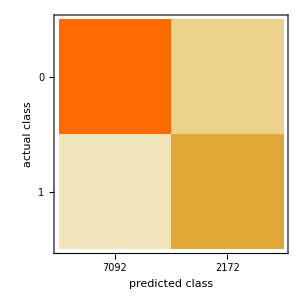
```mathematica
ClassifierMeasurements[train888,validateSetRule, {"ConfusionMatrixPlot","Accuracy","Precision","Recall","FScore"}]
{-Graphics-,0.9843480138169257,<|0->0.9812941665511986,1->0.995114802149487|>,<|0->0.9985899605188945,1->0.9378453038674033|>,<|0->0.9898665175763505,1->0.9656316662716282|>}
```

test model performance with datatest

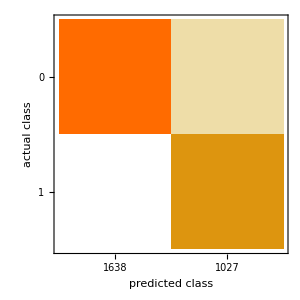
```mathematica
ClassifierMeasurements[train888,datasetRule, {"ConfusionMatrixPlot","Accuracy","Precision","Recall","FScore"}]
{-Graphics-,0.9793621013133208,<|0->0.96751329001772,1->1.|>,<|0->1.,1->0.9464459591041869|>,<|0->0.9834884419093367,1->0.9724862431215607|>}
```

### Find Best Dates Combination

Find all performances starting from February 11th to February 16

```mathematica
s = {validateDate11,validateDate12,validateDate13,validateDate16,validateDate17}
Table[Table[trainTV =NetTrain[trainer,s[[i]],ValidationSet->s[[k]]] ;
c = ClassifierMeasurements[trainTV,datasetRule,"Accuracy"];
{i,k,c},{k,i+1,5}],{i,4}]
(*export to excel to clean and make it nice looking *)
Export["Selection.xls",Grid[Flatten[%,1]],"XLS"]
```

Find all performances starting from February 17 to February 12

```mathematica
s = Reverse[{validateDate11,validateDate12,validateDate13,validateDate16,validateDate17}]
Table[Table[trainTV =NetTrain[trainer,s[[i]],ValidationSet->s[[k]]] ;
c = ClassifierMeasurements[trainTV,datasetRule,"Accuracy"];
{i,k,c},{k,i+1,5}],{i,4}]
Export["Selection2.xls",Grid[Flatten[%,1]],"XLS"]
```

## Random Forest and KNN

Random Forest

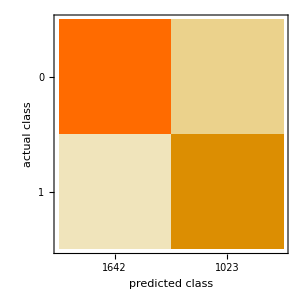
{-Graphics-,0.978612,<|0→0.968104,1→0.996914|>,<|0→0.998173,1→0.947214|>,<|0→0.982909,1→0.971429|>}

```mathematica
c= Classify[trainingSetRule,ValidationSet->testingSetRule,Method->"RandomForest"];
ClassifierInformation[c];
ClassifierMeasurements[c,datasetRule, {"ConfusionMatrixPlot","Accuracy","Precision","Recall","FScore"}]
```

K Nearest Neighbor

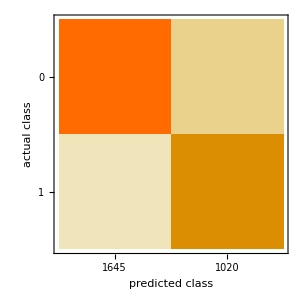
{-Graphics-,0.978236,<|0→0.968695,1→0.994856|>,<|0→0.99696,1→0.948039|>,<|0→0.982624,1→0.970884|>}

```mathematica
c= Classify[trainingSetRule,ValidationSet->testingSetRule,Method->"NearestNeighbors"];
ClassifierInformation[c];
ClassifierMeasurements[c,datasetRule, {"ConfusionMatrixPlot","Accuracy","Precision","Recall","FScore"}]
```